```mathematica
ClearAll["Global`*"];
```

### ステレオビジョンの実装方法

```mathematica
O2={0,b,0};
(*Ly=f*2*Sqrt[3];*)
Ly=2*f*Tan[HFOV/2];
(*Lz=f*Sqrt[3]*9/8;*)
Lz=Ly/ar;
L={Lx,Ly,Lz};
R={Rx,Ry,Rz};
uO=-{f,Ly/2,Lz/2};
p={0,py,pz};
q={0,qy,qz};
v1x=(f*Ry*b)/(Ly*(qy-py))
FullSimplify[1/2*(O2-v1x/f*((L/R)*(p+q)+2*uO))]
```

(b Ry Cot[HFOV/2])/(2 (-py+qy))

{(b Ry Cot[HFOV/2])/(-2 py+2 qy),(2 b py-b Ry)/(2 py-2 qy),(b Ry (pz+qz-Rz))/(2 ar (py-qy) Rz)}

### ステレオビジョン精度について

(1. r^2)/(33255.4+r)

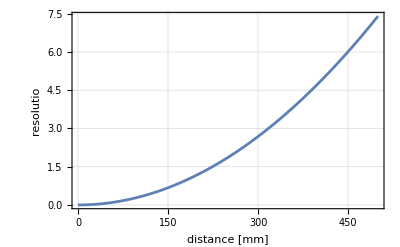

```mathematica
Ry=1920;
b=60(*mm*);
Ly=2*f*Tan[HFOV/2];
HFOV=120*(π/180);
(*f*Ry*b/(Ly*dp)==rを解くと*)
dp=f*Ry*b/Ly/r;
(*dpとdp+1によるx方向の水底位置の差が，このrに対する解像度だ*)
Simplify[f*Ry*b/Ly*(1/dp-1/(dp+1))]
Plot[%,{r,0,500},
Frame->True,
GridLines->Automatic,
FrameLabel->{"distance [mm]","resolutio in dept"}]
```

```mathematica
(*(f*Ry*b)/(Ly*(qy-py))この形から，差(qy-py)が大きいとき，その状態からの少しのズレはとても小さい．例えば(f*Ry*b)/(Ly*Ry)と(f*Ry*b)/(Ly*(Ry+1))の差は小さいので，この位置付近での精度はとても高い*)
```

(17 π)/36

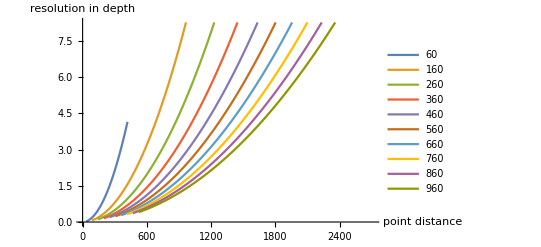

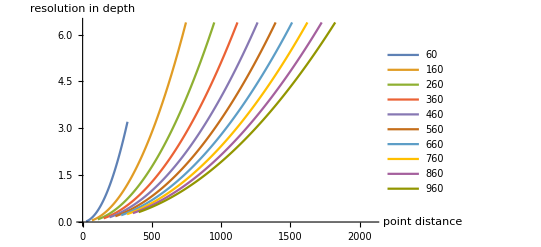

```mathematica
ClearAll["Global`*"];
Ry=1280;
f=1.8;
(*HFOV=120/180*π*)
HFOV=85/180*π
Ly=2*f*Tan[HFOV/2];
(*v1x[py_,qy_]:=If[py==qy,0,(f*Ry*b)/(Ly*(qy-py))];*)
v1x[disparity_,b_]:=If[disparity==0,0,(f*Ry*b)/(Ly*(disparity))];
v1y[py_,disparity_,b_]:=If[disparity==0,0,-b(2  py- Ry)/(2 disparity)];

listb=Table[b,{b,60,1000,100}];
ListPlot[Table[{v1x[disparity,b],v1x[disparity,b]-v1x[disparity+1,b]},{b,listb},{disparity,100,Ry,5}],
AxesLabel->{"point distance","resolution in depth"},
(*PlotRange->{{0,2000},{0,10}},*)
PlotLegends->listb,
Joined->True]

py=10;
ListPlot[Table[{v1y[py,disparity,b],v1y[py,disparity,b]-v1y[py,disparity+1,b]},{b,listb},{disparity,100,Ry,5}],
AxesLabel->{"point distance","resolution in depth"},
(*PlotRange->{{0,2000},{0,10}},*)
PlotLegends->listb,
Joined->True]
```

```mathematica
Table[v1x[py,qy],{py,0,100,1},{qy,0,100,1}]
```

```mathematica
ClearAll["Global`*"];
Manipulate[
f=0.6;
b=0.2;
o1={0,0,0};
o2={0,b,0};
v1={x,y,z};
v2=v1-o2;
v1nl=-v1;
v2nl=-v2;
p1=(-v1nl*f)/v1nl[[1]];
p2=(-v2nl*f)/v2nl[[1]];
xp=(f*o2[[2]])/(p2[[2]]-p1[[2]]);
u=(-v1nl*f)/v1nl[[1]];
opt={Frame->True,PlotRange->{{-1,1},{-1,1}},ImageSize->Large,PlotMarkers->{"OpenMarkers",Large}};
pixelImgs={ListPlot[{{p1[[2]],p1[[3]]}},PlotStyle->{Blue},Evaluate@opt],ListPlot[{{p2[[2]],p2[[3]]}},PlotStyle->{Orange},Evaluate@opt]};
{Row[pixelImgs],
Show[
ListPointPlot3D[{v1,FrameLabel->Automatic},
PlotRange->{{-2,2},{-2,2},{-2,2}}],
Graphics3D[
{{Blue,PointSize[Large],Point[p1]},
{Black,PointSize[Large],Point[o1]},
Arrow[{o1,o1+v1}],
{Blue,Arrow[{o1,o1+p1}]},
{Opacity[0.],EdgeForm[{Thick,Blue}],Blue,Polygon[{{-f,-1,-1},{-f,1,-1},{-f,1,1},{-f,-1,1}}]}
}],
Graphics3D[{{Orange,PointSize[Large],Point[p2+o2]},
{Black,PointSize[Large],Point[o2]},
Arrow[{o2,o2+v2}],
{Orange,Arrow[{o2,o2+p2}]},
{Opacity[0],EdgeForm[{Thick,Orange}],Orange,Polygon[{{-f,-1,-1}+o2,{-f,1,-1}+o2,{-f,1,1}+o2,{-f,-1,1}+o2}]}
}],
ImageSize->Large,
PlotLabel->Style["{x,y,z}="<>ToString[u*xp/u[[1]]]]
]}
,{x,10^-10,1,0.01},{y,-1,1,0.01},{z,-1,1,0.1}]
```